```mathematica
Subsets[Range[5],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

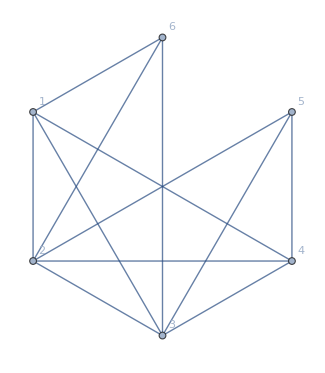
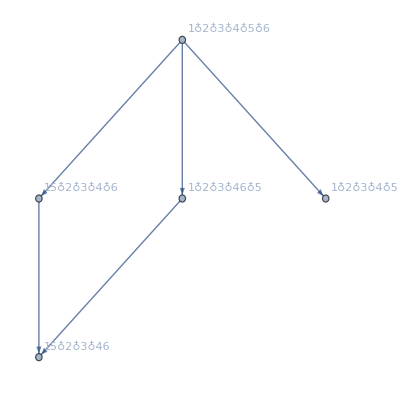
-Graphics-<->-Graphics-

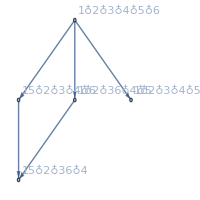
-Graphics-<->-Graphics-

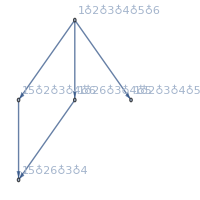
-Graphics-<->-Graphics-

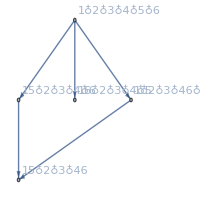
-Graphics-<->-Graphics-

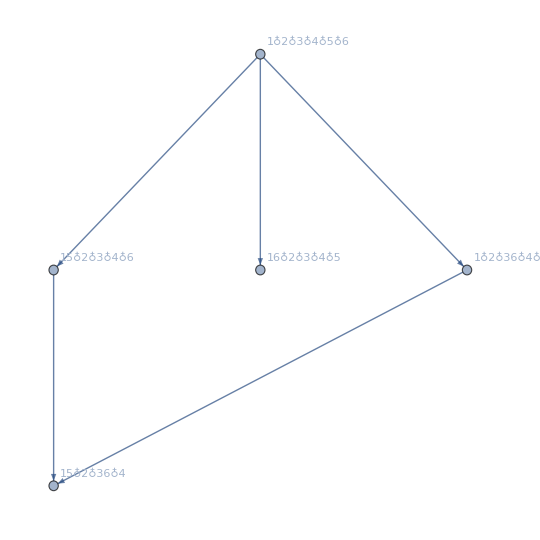
-Graphics-<->-Graphics-

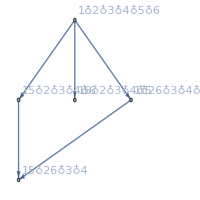
-Graphics-<->-Graphics-

|  |  |  |  |  |  |  |  |

```mathematica
Multicolumn[With[
{nodes=6},With[{edges=Subsets[Range[nodes],{2}]},
Select[
Table[
With[{g=Graph[Range[nodes],s,VertexLabels->"Name",GraphLayout->"CircularEmbedding",ImageSize->70]},
If[MaximalPlanarQ[g]&&!EdgeQ[g,1<->5]&&IsomorphicGraphQ[VertexDelete[g,6],EdgeDelete[CompleteGraph[5],1<->5]],Print[g<->FormulaGraph[FindFullFormula[g]]],Null]
],{s,Subsets[edges]}
],
#≠Null&
]
]
],10]
```

-Graphics-<->-Graphics-

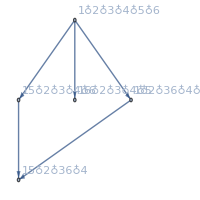
-Graphics-<->-Graphics-

-Graphics-<->-Graphics-

|  |  |  |  |  |  |  |  |

```mathematica
Multicolumn[With[
{nodes=7},With[{edges=Select[Subsets[Range[nodes],{2}],#≠{1,5}&&#≠{1,6}&], comp=EdgeDelete[CompleteGraph[5],1<->5]},
Select[
Monitor[
Table[
With[{g=Graph[Range[nodes],s,VertexLabels->"Name",GraphLayout->"CircularEmbedding",ImageSize->70]},
If[MaximalPlanarQ[g]&&IsomorphicGraphQ[VertexDelete[g,Range[6,nodes]],comp],Print[g<->FormulaGraph[FindFullFormula[g]]],Null]
],{s,Subsets[edges]}
],
s],
#≠Null&
]
]
],10]
```

```mathematica
Length[Subsets[Range[7],{2}]]
```

21

```mathematica
Range[6,6]
```

{6}